# Inlämningsuppgift 1: Problemlösning

IX1307 Problemlösning i Matematik, Inlämningsuppgift 1a, HT2019

Samuel Ferrara

## 1. Inledning

Detta dokument är en inlämningsuppgift som är del av kursen Problemlösning i matematik IX 1307. Uppgiften går ut på att lösa ett antal matematiska problem med hjälp av Mathematica och skriva en kort rapport.

## 2. Nyttiga funktioner i Mathematica

Här är en kort beskrivning av några funktioner som kan vara nyttiga att känna till för att lösa problemen nedan. För mer information om funktionerna se Wolfram Documentation under hjälp-menyn.

#### Ekvationer och Olikheter

Studera följande hjälpfiler i Wolfram Documentation: 
"tutorial/Equations"paclet:tutorial/Equations
"tutorial/SolvingEquations"paclet:tutorial/SolvingEquations
Ta reda på hur kommandona Solve, Reduce, och Eliminate fungerar.
Titta sedan närmare på "tutorial/Inequalities-ManipulatingEquationsAndInequalities"paclet:tutorial/Inequalities-ManipulatingEquationsAndInequalities
för hur man löser olikheter och ekvationer med absolutbelopp.

Exempelvis för att lösa ekvationen |x-4|=4 kan man använda funktionen Reduce.

```mathematica
Reduce[Abs[x-4]==4, x, Reals]
```

x==0||x==8

Reals talar om vilken typ av tal som avses för x. Domänen kan vara Heltal (Integers), Reella tal (Reals) eller Komplexa tal (Complex).

#### Komplexa tal

Den imaginära enheten representeras av ett versalt I i Mathematica.

```mathematica
I*I
```

Roten av ett negativt tal :

```mathematica
Sqrt[-4]
```

Algebra med komplexa tal fungera som vanligt:

```mathematica
(4+3 I)/(2-I)
```

```mathematica
z1=Exp[2+9 I]
```

Funktionen N kan användas för att beräkna numeriska närmevärde av exempelvis z_1

```mathematica
N[z1]
```

eller av andra tal. Här är Pi med 50 siffrors noggranhet:

```mathematica
N[Pi, 50]
```

Olika funktioner kan sedan användas för att manipulera komplexa tal:

```mathematica
z2=4+3I;
```

Realdel:

```mathematica
Re[z2]
```

Imaginärdel

```mathematica
Im[z2]
```

Komplexa konjugatet till z_2

```mathematica
Conjugate[z2]
```

och till z_1

```mathematica
Conjugate[z1]
```

Absolutbeloppet till z_2

```mathematica
Abs[z2]
```

Argumentet till z_1

```mathematica
Arg[z2]
```

För att grafiskt representera komplexa talplanet används ListPlot. Vi börjar med att skapa en lista av talen:

```mathematica
cn={z1, Conjugate[z1], z2, Conjugate[z2]}
```

Sedan kan listan av tal konverteras till en list av talpar {realdel, imaginärdel}

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i, 1, 4}]
```

Här är en de komplexa talen ritade i det komplexa talplanet:

```mathematica
ListPlot[pp, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ EdgeForm[Red],FaceForm[],Rectangle[{pp[[3,1]], pp[[3,2]]}, {pp[[2, 1]], pp[[2, 2]]}], }]
```

#### Summor

Sum används för att en serie, dvs en summa av en talföljd. Om det finns ett utryck för varje element i serien kan den skrivas enligt:

```mathematica
Sum[n^2, {n, 1, 10}]
```

I detta fall serien för talföljden n^2 där n∈[1, 10].
Om man vill summera de 100 första primtalen så kan man använda funktionen Prime. För att bestämma det 10:e primtalet kan man använda

```mathematica
Prime[10]
```

Funktionen Sum kan då användas för att beräkna serien av de 100 första primtalen.

```mathematica
Sum[Prime[i], {i, 1, 100}]
```

## 3. Problem

Lös nedanstående problem. Problemets lösning och resultat skall innehålla visualisering där det är relevant.

### Polynomekvation

Hitta lösningarna till polynomekvationen: 2/3 x^5-2/3 x^4-8 x^3+8 x^2+18x-18=0. 
Rita också grafen för polynomet och markera nollställen med en röd punkt.

#### Problemformulering

Uppgiften går ut på att lösa en polynomekvation av femte graden, och visiualisera lösningen genom att markera funktionens eventuella nollställen med röda punkter i dess graf. Vad som söks är de punkter där funktionens graf skär x-axeln, med andra ord då y=0. Ett polynom av femte graden har maximalt fem reella lösningar, vilket innebär att dess graf inte kan skära x-axeln på fler än fem ställen.

#### Lösning

(1) Det första steget i lösningen är att en funktion för en godtycklig variabel x defineras.

```mathematica
f[x_]=2/3 x^5-2/3 x^4-8  x^3+8x^2+18x-18
```

-18+18 x+8 x^2-8 x^3-(2 x^4)/3+(2 x^5)/3

(2) Därefter beräknas funktionens nollställen, dvs y-värdena då x=0 med funktionen. Där det anges att x1, x2, x3, x4 och x5 är element i x.

```mathematica
{x1,x2,x3,x4,x5}=x/.Solve[f[x]==0]
```

{-3,1,3,-√3,√3}

(3) Resultatet visualiseras genom att funktionens graf ritas upp med hjälp av funktionen “Plot”, xy-koordinaterna grafens skärningspunkter med y-axeln visualiseras även för att förtydliga sambandet mellan de röda prickarna och polynomekvationens beräknade resultat.

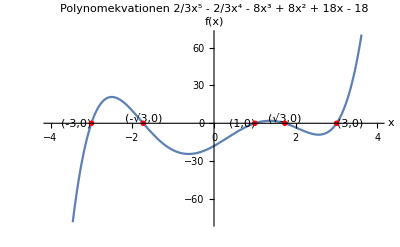

```mathematica
Plot[f[x],{x,-4,4},AxesLabel-> {"x","f(x)"}, PlotLabel -> "Polynomekvationen 2/3x^5 - 2/3x^4 - 8x^3 + 8x^2 + 18x - 18", Epilog -> {Text ["(-3,0)",{x1,f[x1]},Right],Text ["(1,0)",{x2,f[x2]},Right],Text ["(3,0)",{x3,f[x3]},Left],Text ["(-√3,0)",{x4,f[x4]},Bottom],Text ["(√3,0)",{x5,f[x5]},Bottom],
PointSize[0.01],Red,Point[{{x1,f[x1]},{x2,f[x2]},{x3,f[x3]},{x4,f[x4]},{x5,f[x5]}}]}]
```

### Ekvation med absolutbelopp

Lös ekvationen  |x-1|+|x-3|=4. Illustrera lösningsområdet grafiskt.

#### Problemformulering

Uppgiften går ut på att lösa ekvationen|x-1|+|x-3|=4 absolutbelopp. För att lösa ekvationen behöver man ta reda på för vilka x det gäller att summan av de två absolutbeloppen är fyra.

Enligt definitionen av absolutbelopp gäller det att:

|x-1|=Piecewise[{{X-1,, då x-1≥0}, {-(x-1),, då x-1<0}}]
|x-3|=Piecewise[{{x-3,, då x-3≥0}, {-(x-3),, då x-3<0}}]

#### Lösning

(1) Funktionen defineras för ett godtyckligt x

```mathematica
g[x_]:=Abs[x-1]+Abs[x-3]
```

(2) Då x<1 så är ekvationen ekvivalent med -(x-1)-(x-3)==4 vilket ger x=0 . Eftersom x = 0 < 1, så kan det konstateras att en lösning har funnits.

(3) Då x ≥ 3 så är ekvationen ekvivalent med (x-1)+(x-3)=4, vilket ger x=4. Eftersom x=4≥3 så kan det konstateras att en lösning har funnits.

```mathematica
Solve[-(x-1)-(x-3)==4]
```

{{x→0}}

```mathematica
Solve[(x-1)+(x-3)==4]
```

{{x→4}}

```mathematica
{x1,x2}=x/.Solve[g[x]==4,x]
```

{0,4}

```mathematica
Reduce[g[x]==4,x,Reals]
```

x==0||x==4

(4) Lösningsområdet för ekvationen Illustreras sedan med kommandot “Plot”, punkterna där summan av absolutbeloppen är likamed fyra visualiseras med röda prickar.

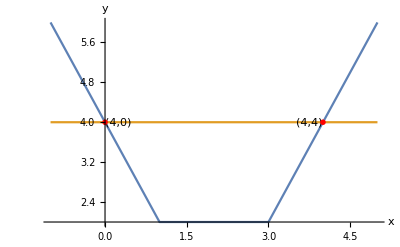

```mathematica
Plot[{g[x],4} ,{x,-1,5},AxesLabel->{x,y} , Epilog -> {Text ["(4,0)",{x1,g[x1]},Left],Text ["(4,4)",{x2,g[x2]},Right],
PointSize[0.01],Red,Point[{{x1,g[x1]},{x2,g[x2]}}]}]
```

### Binomisk ekvation

Finn lösningen till ekvationen z^7=2-i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

#### Problemformulering

Uppgiften går ut på att hitta lösningarna till ekvationen z^7=2-i och visualisera dess lösningar som par av koordinater på det komplextalplanet, där varje par befinner sig på ett lika stort avstånd från Origo.

#### Lösning

(1) Ekvationen har exakt sju lösningar. Dessa sju lösningar har en reell del och en imaginär del och fås genom att lösa ekvationen med kommandot “Solve”.

```mathematica
Z=z/.Solve[z^7==2-ⅈ]
```

{(2-ⅈ)^(1/7),-(-1)^(1/7) (2-ⅈ)^(1/7),(-1)^(2/7) (2-ⅈ)^(1/7),-(-1)^(3/7) (2-ⅈ)^(1/7),(-1)^(4/7) (2-ⅈ)^(1/7),-(-1)^(5/7) (2-ⅈ)^(1/7),(-1)^(6/7) (2-ⅈ)^(1/7)}

(2) De sju lösningarna listas sedan som par av koordinater på det komplexa talplanet, varje punkts avstånd från Orgio är lika med absolutbeloppet av Z.

```mathematica
Abs[Z]
```

{5^(1/14),5^(1/14),5^(1/14),5^(1/14),5^(1/14),5^(1/14),5^(1/14)}

```mathematica
list=Table[{Re[Z[[ⅈ]]],Im[Z[[ⅈ]]]},{ⅈ,1,Length[Z]}]
```

{{Re[(2-ⅈ)^(1/7)],Im[(2-ⅈ)^(1/7)]},{Re[-(-1)^(1/7) (2-ⅈ)^(1/7)],Im[-(-1)^(1/7) (2-ⅈ)^(1/7)]},{Re[(-1)^(2/7) (2-ⅈ)^(1/7)],Im[(-1)^(2/7) (2-ⅈ)^(1/7)]},{Re[-(-1)^(3/7) (2-ⅈ)^(1/7)],Im[-(-1)^(3/7) (2-ⅈ)^(1/7)]},{Re[(-1)^(4/7) (2-ⅈ)^(1/7)],Im[(-1)^(4/7) (2-ⅈ)^(1/7)]},{Re[-(-1)^(5/7) (2-ⅈ)^(1/7)],Im[-(-1)^(5/7) (2-ⅈ)^(1/7)]},{Re[(-1)^(6/7) (2-ⅈ)^(1/7)],Im[(-1)^(6/7) (2-ⅈ)^(1/7)]}}

(3) Listan med koordinater plottas sedan tillsammans med en cirkel som har mittpunkt i origo och radien 5^(1/14) vilket visar att alla lösningar till ekvationen befinner sig på samma avstånd från origo på en cirkel med mittpunkt i origo.

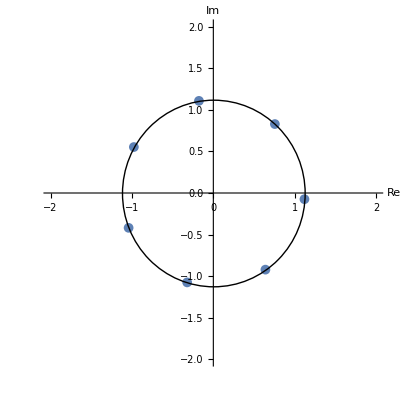

```mathematica
ListPlot[list,AxesLabel-> {"Re","Im"},PlotRange-> {{-2,2},{-2,2}},AspectRatio-> {Automatic,Medium},PlotMarkers -> {Automatic, Medium},Epilog-> {Circle[{0,0},5^(1/14)]}]
```

### Akilles och sköldpaddan

En paradox är ett påstående som förefaller korrekt utifrån sanna antaganden men leder till självmotsägelser eller till logiskt oacceptabla slutsatser [Wikipedia]. 

Akilles och sköldpaddan är en av Zenons paradoxer. Antag att Akilles springer 10 gånger så fort som sköldpaddan. De båda skall tävla vem som först kommer i mål på 100 meter. Då sköldpaddan är långsammare än Akilles så får den ett försprång på 80 meter. Paradoxen är att när Akilles har sprungit dessa 80 meter, så har sköldpaddan kommit 8 meter, när Akilles har sprungit dessa 8 meter har sköldpaddan kommit 8 dm. Det resonemanget skulle leda till att Akilles aldrig kommer i kapp sköldpaddan. 

Undersök och förklara paradoxen genom att rita tid-sträcka grafer för Akilles och Sköldpaddan. Dessutom beskriv en formel för talföljden ovan och beräkna serien för den med hjälp av Mathematica.

När kommer Akilles i kapp sköldpaddan? 

Visa paradoxen både numeriskt och grafiskt.

#### Problemformulering

Tid och hastighet är okända, det anges att Achilles hastighet är 10 gånger  Sköldpaddans och hastigheterna antas vara konstanta. Paradoxen ska visas både numeriskt och grafiskt.

#### Lösning

(1) Det resonemang som ger upphov till paradoxen är att sköldpaddan alltid kommer att ligga före achilles med följande sträcka om sköldpaddan börjar på 80 meters avstånd.

```mathematica
summaS=sum[80*(1/10)^(n-1)]
```

sum[2^(5-n) 5^(2-n)]

```mathematica
h[x_]:=GeneratingFunction[summaS,n,x]
```

```mathematica
Table[summaS,{n,1,20}]
```

{sum[80],sum[8],sum[4/5],sum[2/25],sum[1/125],sum[1/1250],sum[1/12500],sum[1/125000],sum[1/1250000],sum[1/12500000],sum[1/125000000],sum[1/1250000000],sum[1/12500000000],sum[1/125000000000],sum[1/1250000000000],sum[1/12500000000000],sum[1/125000000000000],sum[1/1250000000000000],sum[1/12500000000000000],sum[1/125000000000000000]}

(2) I takt med att tiden går mot oändligheten, så går avståndet mellan achilles och sköldpaddan mot noll. Detta illustreras i grafen nedan.

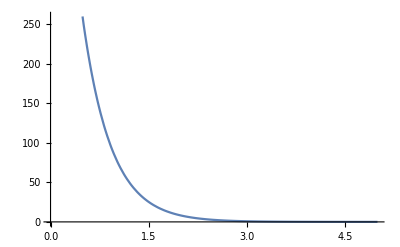

```mathematica
Plot[{80 (1/10)^(n-1)} ,{n,0,5}]
```

(3) Akilles kommer ikapp sköldpaddan efter 800 sträck-enheter.

```mathematica
∑_(n=1)^∞ 2^(5-n) 5^(2-n)
```

800/9

(4) Detta kan även beskrivas grafiskt, eftersom hastigheterna är konstanta kan förändringen av postion över tid beskrivas med räta linjens ekvation enligt följande

s(t)=10v*t+s_0
s_a(x)=10x+0
s_s(x)=10x+80

```mathematica
s[x_]:=10 *x+0;
```

```mathematica
a[x_]:=x+80;
```

(5) Hur många tidsenheter som passerar innan Akilles kommer ikapp sköldpaddan fås sedan av följande

```mathematica
{x1}=x/.Solve[s[x]==a[x]]
```

{80/9}

```mathematica
N[x1]
```

{8.88889}

(6) När tidenheten är beräknad kan sedan positionen beräknas.

```mathematica
s[x1]
```

{800/9}

```mathematica
N[{800/9}]
```

{88.8889}

(7) Denna punkt illustreras grafiskt i ett sträcka-tid diagram genom att funktionen plottas och skärningspunkten markeras med en röd prick.

```mathematica
Sköldpadda=Plot[{a[x],s[x]},{x,0,15},AxesOrigin -> {0,0},AxesLabel -> {"Tid","Sträcka[m]"}, PlotLabels-> {"Sköldpaddan","Akilles"},Epilog -> {Text ["(80/9,800/9)",{x1,s[x1]},Bottom],PointSize[0.02],Red,Point[{x1,s[x1]}]}]
```

-Graphics-

```mathematica
nb=NotebookOpen["/Users/chris/Documents/notebook.nb"];
Export[FileNameJoin[{$InitialDirectory,"Inlamning1.pdf"}],nb]
```